```mathematica
xl[t_]= x[t] + (d - (l[t]- h) Tan [theta[t]]) Cos [theta[t]];
yl[t_]= x[t] + (l[t] - h) Cos[theta[t]] + d Sin[theta[t]];

xw[t_]= x[t] - (dw -d) Cos[theta[t]];
yw[t_]= y[t] -(dw -d) Sin[theta[t]];

xp[t_]= x[t] + d Cos[theta[t]];
yp[t_]= y[t] + d Sin[theta[t]];

T = 1/2 mw (xw'[t]^2 + yw'[t]^2) +  1/2 mp (xp'[t]^2 + yp'[t]^2) +  1/2 ml (xl'[t]^2 + yl'[t]^2) + 1/2 Iw (phi'[t] + theta'[t])^2 + 1/2 Ib theta'[t]^2;
V = g(ml yl[t] + mw yw[t] + mp yp[t]) + 1/2 K (l[t] - l0)^2;
eqConstraintStance = y ->  Function[t, (len - l[t] - d Sin[theta[t]]) Cos[theta[t]]];
eqConstraintSpring1 = l -> Function[t, l0];
eqConstraintSpring2 = l -> Function[t, lmax];

L = T -V;
L = L /. eqConstraintStance;

eq1 = D[D[L, D[x[t], t]], t] == D[L, x[t]];
eq2 = D[D[L, D[l[t], t]], t] == D[L, l[t]];
eq3 = D[D[L, D[theta[t], t]], t] == D[L, theta[t]];
eq4 = D[D[L, D[phi[t], t]], t] == D[L, phi[t]];
eqStance = {eq1, eq2, eq3, eq4};

L = T - V;
eq1 = D[D[L, D[x[t], t]], t] == D[L, x[t]];
eq2 = D[D[L, D[y[t], t]], t] == D[L, y[t]];
eq3 = D[D[L, D[l[t], t]], t] == D[L, l[t]];
eq4 = D[D[L, D[theta[t], t]], t] == D[L, theta[t]];
eq5 = D[D[L, D[phi[t], t]], t] == D[L, phi[t]];
eqFlight = {eq1, eq2, eq3, eq4, eq5};

L = T -V;
L = L /. eqConstraintSpring1;

eq1 = D[D[L, D[x[t], t]], t] == D[L, x[t]];
eq2 = D[D[L, D[y[t], t]], t] == D[L, y[t]];
eq3 = D[D[L, D[theta[t], t]], t] == D[L, theta[t]];
eq4 = D[D[L, D[phi[t], t]], t] == D[L, phi[t]];
eqSpring1 = {eq1, eq2, eq3, eq4};

L = T -V;
L = L /. eqConstraintSpring2;

eq1 = D[D[L, D[x[t], t]], t] == D[L, x[t]];
eq2 = D[D[L, D[y[t], t]], t] == D[L, y[t]];
eq3 = D[D[L, D[theta[t], t]], t] == D[L, theta[t]];
eq4 = D[D[L, D[phi[t], t]], t] == D[L, phi[t]];
eqSpring2 = {eq1, eq2, eq3, eq4};

values = {mw -> 1.5, mp -> 2.5, ml -> 0.7, Iw -> 1.5*0.6*0.6/2, Ib -> 0.5, K -> 500, l0 -> 0.2, h -> 0.3, d-> 0.1, dw -> 0.2, g-> 9.8, len -> 0.5, lmax -> 0.4};
eqStance = eqStance /. values;
eqFlight = eqFlight /. values;
eqSpring1 = eqSpring1 /. values;
eqSpring2 = eqSpring2 /. values;
```

{0.310178,0.290726,0.487914,0.093095,0.473976,0.199602,-1.49279,0.492794}

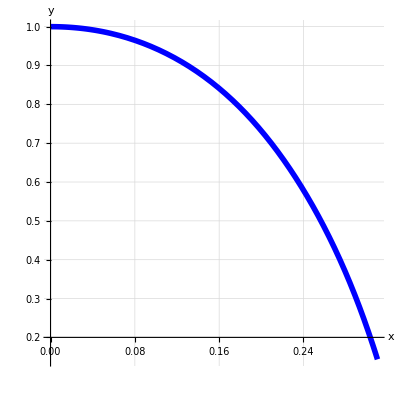

```mathematica
start = 0;
initFlight ={ x[0] == 0, y[0] == 1, l[0] == 0.3, theta[0] == 1, phi[0] == 0, x'[0]== 1, y'[0]== 0, l'[0] == 0, theta'[0] == -1, phi'[0] == 0};
solveForFlight = {x, y, l, theta, phi};

solFlight = First[NDSolve[Join[eqFlight, initFlight], solveForFlight, {t, 0, 1}, Method -> {"EventLocator", "Event" -> (y[t] - (len - l[t] - d Sin[theta[t]]) Cos[theta[t]]) /. values, "EventAction" :> Throw[end = t, "StopIntegration"]}]];
endFlight =  Evaluate[{x[end], l[end], theta[end], phi[end], x'[end], l'[end], theta'[end], phi'[end]} /. solFlight]
ParametricPlot[Evaluate[{x[t], y[t]} /. solFlight], {t, start, end}, AxesLabel -> {x, y}, LabelStyle -> Directive[Black, Bold], PlotStyle -> {Blue, Thickness[0.01]},GridLines -> Automatic, GridLinesStyle -> Directive[Dashed], AspectRatio -> 1 ]
```

{0.0658856,0.135001,0.316646,0.385884,-0.00246545,0.880769,-0.212161,0.442078,-1.40326,-0.0895323}

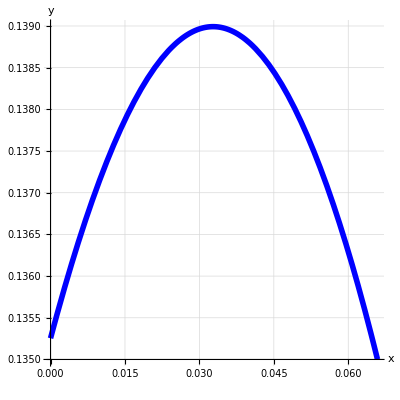

```mathematica
start = 0;
end = 0.07;
initStance = { x[0] == 0, l[0] == 0.3, theta[0] ==  thetaEnd, phi[0] == 0, x'[0]== 1, l'[0] == 0, theta'[0] == thetadotEnd, phi'[0] == 0};
solveForStance = {x, l, theta, phi};

tempY[t_] = ((len - l[t] - d Sin[theta[t]]) Cos[theta[t]] /. values);
tempYdot[t_] = D[tempY[t], t];

solStance = First[NDSolve[Join[eqStance, initStance], solveForStance, {t, 0, end}]];
endStance =  Evaluate[{x[end], tempY[end], l[end], theta[end], phi[end], x'[end], tempYdot[end], l'[end], theta'[end], phi'[end]} /. solStance]
ParametricPlot[Evaluate[{(x[t])/.solStance, tempY[t] /. solStance}], {t, start, end}, AxesLabel -> {x, y}, LabelStyle -> Directive[Black, Bold], PlotStyle -> {Blue, Thickness[0.01]},GridLines -> Automatic, GridLinesStyle -> Directive[Dashed], AspectRatio -> 1 ]
```